```mathematica
ClearAll["Global`*"];
```

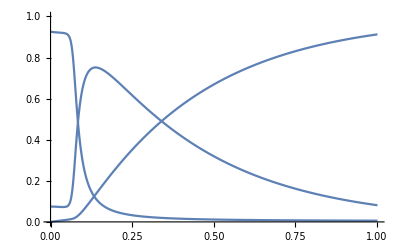

```mathematica
SetDirectory[NotebookDirectory[]];
L1=10.;
L2=10.;
N1=41;N2=N1;
h1=N[L1/(N1-1)];
h2=N[L2/(N2-1)];
K=700;
x1=Table[k h1,{k,0,N1}];
x2=Table[k h2,{k,0,N2}];
plotMax = 1.2;
SIR = Import["SIR_midd.dat","Data"];
sm={};
im={};
rm={};
tend=SIR[[K,1]];
For[k=1,k≤K+1,k++,
N0=SIR[[k,2]]+SIR[[k,3]]+SIR[[k,4]];

sm=Append[sm,N[{SIR[[k,1]]/tend,SIR[[k,2]]/N0}]];
im=Append[im,N[{SIR[[k,1]]/tend,SIR[[k,3]]/N0}]];
rm=Append[rm,N[{SIR[[k,1]]/tend,SIR[[k,4]]/N0}]];
];
For[k=1,k≤K+1,k++,
SIR[[k,1]]=sm[[k,1]];
SIR[[k,2]]=sm[[k,2]];
SIR[[k,3]]=im[[k,2]];
SIR[[k,4]]=rm[[k,2]];
];
Export["origin.dat",SIR];
Show[ListLinePlot[im,PlotRange->{0,1}],ListLinePlot[sm,PlotRange->{0,1}],ListLinePlot[rm,PlotRange->{0,1}]]
```

```mathematica
(*SSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSSS*)
```

```mathematica
S={};
For[numF=0,numF≤K,numF++,
s=Import["S_layer_"<>ToString[numF] <>".dat","Data"];
ss={};
For[i=1,i≤N1,i++,
For[j=1,j≤N2,j++,
ss=Append[ss,{x1[[i]],x2[[j]],s[[i,j]]*8}];
];
];
S=Append[S,ss];
];
```

```mathematica
Splot=Table[ListPlot3D[S[[k]],PlotRange->{0,1},PlotStyle->Directive[Green],LabelStyle->Directive[15],AxesLabel->(Style[#,17,Bold,Italic]&/@{"x_1","x_2","P_S"}),AxesStyle->Thick,ImageSize->500,ViewPoint->{Pi,Pi/2,1}(*ViewPoint->{0,-1.5,0.5}{Pi,Pi/2,1}*),Boxed->False],{k,1,K+1}];
```

```mathematica
Animate[Splot[[k]],{k,1,K+1,1},AnimationRunning->False]
```

```mathematica
Splot[[150]]
```

-Graphics3D-

```mathematica
Export["S_k=0.jpg",Splot[[1]]]
```

S_k=0.jpg

```mathematica
(*IIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIIII*)
```

```mathematica
Inf={};

For[numF=0,numF≤K,numF++,
inf=Import["I_layer_"<>ToString[numF] <>".dat","Data"];
ii={};
For[i=1,i≤N1,i++,
For[j=1,j≤N2,j++,
ii=Append[ii,{x1[[i]],x2[[j]],inf[[i,j]]*5}];
];
];
Inf=Append[Inf,ii];
];
```

```mathematica
Iplot=Table[ListPlot3D[Inf[[k]],PlotRange->{0,1},PlotStyle->Directive[Red],LabelStyle->Directive[15],AxesLabel->(Style[#,17,Bold,Italic]&/@{"x_1","x_2","P_I"}),AxesStyle->Thick,ImageSize->500,ViewPoint->{Pi,Pi/2,1}(*ViewPoint->{0,-1.5,0.5}{Pi,Pi/2,1}*),Boxed->False],{k,1,K+1}];
```

```mathematica
Animate[Iplot[[k]],{k,1,K+1,1},AnimationRunning->False]
```

```mathematica
Export["I_k=0.jpg",Iplot[[1]]]
```

I_k=0.jpg

```mathematica
Iplot[[120]]
```

-Graphics3D-

```mathematica
Iplot[[1]]
```

-Graphics3D-

```mathematica
(*RRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRRR*)
```

```mathematica
R={};

For[numF=0,numF≤K,numF++,
r=Import["R_layer_"<>ToString[numF] <>".dat","Data"];
rr={};
For[i=1,i≤N1,i++,
For[j=1,j≤N2,j++,
rr=Append[rr,{x1[[i]],x2[[j]],r[[i,j]]*5}];
];
];
R=Append[R,rr];
];
```

```mathematica
Rplot=Table[ListPlot3D[R[[k]],PlotRange->{0,1},PlotStyle->Directive[Gray],LabelStyle->Directive[15],AxesLabel->(Style[#,17,Bold,Italic]&/@{"x_1","x_2","P_R"}),AxesStyle->Thick,ImageSize->500,ViewPoint->{Pi,Pi/2,1}(*ViewPoint->{0,-1.5,0.5}{Pi,Pi/2,1}*),Boxed->False],{k,1,K+1}];
```

```mathematica
Animate[Rplot[[k]],{k,1,K+1,1},AnimationRunning->False]
```

```mathematica
Export["R_k=100.jpg",Rplot[[100]]]
```

R_k=100.jpg

```mathematica
Rplot[[100]]
```

-Graphics3D-

```mathematica
Export["S1.avi",Splot];
```

```mathematica
Export["I1.avi",Iplot];
```

```mathematica
Export["R1.avi",Rplot];
```

```mathematica
p1=Plot3D[{(0.5)^39(L-x)^2 x^2(L-y)^2 y^2 Exp[-(0.5)^8((x-10)^2+(y-10)^2)] },{x,0,50},{y,0,50},PlotStyle->{Green},LabelStyle->Directive[20],PlotRange->All];p2=Plot3D[{(0.5)^39(L-x)^2 x^2(L-y)^2 y^2 Exp[-(0.5)^3((x-35.)^2+(y-35.)^2)] },{x,0,50},{y,0,50},PlotStyle->{Red},LabelStyle->Directive[20],PlotRange->All];Show[p1,p2]
```

-Graphics3D-

```mathematica
1/(0.5)^39
```

5.49756×10^11

```mathematica
q=ListPlot3D[Inf,PlotStyle->Red,LabelStyle->Directive[20],PlotLegends->{"t=0.5"},PlotRange->All];p=ListPlot3D[S,PlotStyle->Green,LabelStyle->Directive[20],PlotLegends->{"t=0.5"},PlotRange->All];
```

```mathematica
Show[q,p]
```

-Graphics3D-

```mathematica
Show[Plot3D[{25000.*x*(1.-x)*x*(1.-x)*y*(1.-y)*y*(1.-y)*Exp[-50.*((x-0.8)*(x-0.8)+(y-0.5)*(y-0.5))]},{x,0,1},{y,0,1},PlotStyle->{Yellow,Opacity[0.7]},LabelStyle->Directive[20],PlotLegends->{"t=0"},PlotRange->All],(*ListPointPlot3D[p1,PlotStyle->{Green,Opacity[0.7]}],*)ListPlot3D[S,PlotStyle->Green,LabelStyle->Directive[20],PlotLegends->{"t=0.5"},PlotRange->All],(*ListPlot3D[p5,PlotStyle->{Blue,Opacity[0.07]},LabelStyle->Directive[20],PlotLegends->{"t=1.5"}],*)AxesLabel->(Style[#,17,Bold,Italic]&/@{"x","y","u"}),LabelStyle->Directive[15],AxesStyle->Thick,BoxRatios->{1,1,0.6},PlotRange->All,ImageSize->500,Boxed->False]
```

-Graphics3D-

```mathematica
Show[Plot3D[{5000.*x*(1.-x)*x*(1.-x)*y*(1.-y)*y*(1.-y)*Exp[-50.*((x-0.2)*(x-0.2)+(y-0.5)*(y-0.5))]},{x,0,1},{y,0,1},PlotStyle->{Yellow,Opacity[0.7]},LabelStyle->Directive[20],PlotLegends->{"t=0"},PlotRange->All],

ListPlot3D[Inf,PlotStyle->{Red},LabelStyle->Directive[20],PlotLegends->{"t=0.5"},PlotRange->All],AxesLabel->(Style[#,17,Bold,Italic]&/@{"x","y","u"}),LabelStyle->Directive[15],AxesStyle->Thick,BoxRatios->{1,1,0.6},PlotRange->All,ImageSize->500,Boxed->False]
```

-Graphics3D-

```mathematica
Show[Plot3D[{0},{x,0,1},{y,0,1},PlotStyle->{Yellow,Opacity[0.7]},LabelStyle->Directive[20],PlotLegends->{"t=0"},PlotRange->All],

ListPointPlot3D[R,PlotStyle->{Gray,Opacity[0.07]},LabelStyle->Directive[20],PlotLegends->{"t=0.5"}],AxesLabel->(Style[#,17,Bold,Italic]&/@{"x","y","u"}),LabelStyle->Directive[15],AxesStyle->Thick,BoxRatios->{1,1,0.6},PlotRange->All,ImageSize->500,Boxed->False]
```

-Graphics3D-

```mathematica
Plot3D[{500.*x*(1.-x)*x*(1.-x)*y*(1.-y)*y*(1.-y)},{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Splot
```

{-Graphics3D-}

```mathematica
m=Plot3D[30000.x(1.-x)x(1.-x)y(1.-y)y(1.-y)Exp[-90.((x-0.3)(x-0.3)+(y-0.2)(y-0.2))],{x,0,1},{y,0,1},PlotRange->All,ColorFunction->"ValentineTones"]
```

-Graphics3D-

```mathematica
p=Plot3D[35000.*x*(1.-x)*x*(1.-x)*y*(1.-y)*y*(1.-y)*Exp[-15.*((x-0.8)*(x-0.8)+(y-0.8)*(y-0.8))],{x,0,1},{y,0,1},PlotRange->All,ColorFunction->"AuroraColors"]
```

-Graphics3D-

```mathematica
Show[m,p]
```

-Graphics3D-

```mathematica
Gray
```

GrayLevel[0.5]

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
q=0.001;x0=0.5;
Plot3D[1/2(1+(x-x0)/(√((x-x0)^2+q))),{x,-1,1},{y,-1,1},ViewPoint->{3/20,3/2,0.5}]
```

-Graphics3D-

```mathematica
uS[x_,y_]:=Piecewise[{{(Cos[Pi x/10])^2,x>5},{0,x<5}}];
uI[x_,y_]:=Piecewise[{{(Cos[Pi x/8])^2 0.6,x<4},{0,x>4}}];
```

```mathematica
D[(Cos[Pi y/10])^2,y]
```

-1/5 π Cos[(π y)/10] Sin[(π y)/10]

```mathematica
Plot3D[{uS[x,y],uI[x,y]},{x,0,10},{y,0,10},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{0.5^37 x(50-x)x(50-x)y(50-y)y(50-y)Exp[(-((x-25)(x-25)+(y-25)(y-25)))/90]},{x,0,50},{y,0,50},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{0.49^38 x(50-x)x(50-x)y(50-y)y(50-y)Exp[(-((x-25)(x-25)+(y-25)(y-25)))/10]},{x,0,50},{y,0,50},PlotRange->All]
```

-Graphics3D-